# Optimización

Optimización de beneficios

Una empresa comercializa un producto cuya función de demanda es 
P=f(Q)=5700-25Q,
siendo P el precio de venta y Q el número de unidades vendidas. Además, la empresa tiene la siguiente estructura de costes mensuales, en ptas:
- Costes fijos: k.
- Costes de mano de obra: 2 Q^2+100Q.
- Coste de materia prima: 200Q.
Suponiendo que en el mes considerado, la empresa venderá la totalidad de la producción, se pide:

(a) Calcular las funciones de coste variable y de coste total mensuales, sabiendo que, cuando se producen 200 unidades, los costes totales ascienden a 200000 euros.

(b) Determinar el número de unidades que deben venderse para maximizar el beneficio mensual de la empresa. ¿A qué precio deben venderse?

Solución

Definimos la función precio en Mathematica

```mathematica
precio[q_]:=5700-25q
```

El coste variable son todos los costes excepto los fijos, y el coste total son todos.

```mathematica
costev[q_]:=2q^2+100q+200q
costet[q_]:=costev[q]+k
```

Si cuando se producen 200 unidades los costes totales son 200000,

```mathematica
Solve[costet[200]==200000,k]
```

{{k→60000}}

Reevaluamos la función CosteTotal

```mathematica
costet[q_]:=costev[q]+60000
```

Definimos las funciones de ingreso y beneficio

```mathematica
ingreso[q_]:=precio[q]q
beneficio[q_]:=ingreso[q]-costet[q]
```

Como puede verse, el dominio de la función de beneficios corresponderá a todos los valores donde la producción sea positiva, esto es, el intervalo [0,+∞).

Calculamos el máximo de la función de beneficio. Condición de primer orden

```mathematica
beneficio'[q]
D[beneficio[q],{q,1}]
```

5400-54 q

5400-54 q

```mathematica
Solve[beneficio'[q]==0,q]
```

{{q→100}}

Y en dicho valor, la derivada segunda vale ... (Condición de segundo orden)

```mathematica
beneficio''[100]
```

-54

Luego es un máximo relativo. Para ver que es absoluto vamos a calcular la derivada segunda del beneficio

```mathematica
beneficio''[q]
```

-54

que como es negativo y el dominio de la función de beneficios es convexo, la función de beneficio será convexa, y por tanto, el máximo relativo será global. Gráficamente

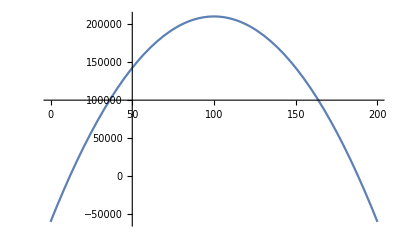

```mathematica
Plot[beneficio[q],{q,0,200},AxesOrigin->{50,100000}]
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

Podemos ver que el beneficio es un máximo absoluto para Q=100.

El precio para la producción que maximiza el beneficio será